## Диффуры

```mathematica
eqs= {Ng1'[t] == 1/2 Γ Ne[t] - σ1 Φ (Ng1[t] - Ne[t]),
Ng2'[t] == 1/2 Γ Ne[t] - σ2 Φ (Ng2[t] - Ne[t]),
Ne'[t] == -Γ Ne[t] + σ1 Φ (Ng1[t] - Ne[t])+σ2 Φ (Ng2[t] - Ne[t])};
```

```mathematica
eqs2 = eqs /. {Γ -> 1., σ1 -> 1., σ2 -> 2., Φ-> 1.}
```

{Ng1'[t]==0.5 Ne[t]-1. (-Ne[t]+Ng1[t]),Ng2'[t]==0.5 Ne[t]-2. (-Ne[t]+Ng2[t]),Ne'[t]==-1. Ne[t]+1. (-Ne[t]+Ng1[t])+2. (-Ne[t]+Ng2[t])}

```mathematica
DSolveValue[eqs2, {Ng1[t], Ng2[t], Ne[t]}, t]
```

{0.4 ⅇ^(-7. t) (-0.557354 ⅇ^(1.32055 t)-0.442646 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[1]+0.4 ⅇ^(-7. t) (0.119107 ⅇ^(1.32055 t)+1.38089 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[2]+0.4 ⅇ^(-7. t) (0.302955 ⅇ^(1.32055 t)-1.30296 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[3],0.333333 ⅇ^(-7. t) (-1.41766 ⅇ^(1.32055 t)+0.417663 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[1]+0.333333 ⅇ^(-7. t) (0.302955 ⅇ^(1.32055 t)-1.30296 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[2]+0.333333 ⅇ^(-7. t) (0.770584 ⅇ^(1.32055 t)+1.22942 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[3],0.266667 ⅇ^(-7. t) (2.60811 ⅇ^(1.32055 t)+0.14189 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[1]+0.266667 ⅇ^(-7. t) (-0.557354 ⅇ^(1.32055 t)-0.442646 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[2]+0.266667 ⅇ^(-7. t) (-1.41766 ⅇ^(1.32055 t)+0.417663 ⅇ^(5.67945 t)+1. ⅇ^(7. t)) C[3]}

## Стационарная картинка

```mathematica
eqs= {0 == 1/2 Γ Ne - σ1 Φ (Ng1 - Ne),
0== 1/2 Γ Ne - σ2 Φ (Ng2- Ne),
0== -Γ Ne + σ1 Φ (Ng1 - Ne)+σ2 Φ (Ng2 - Ne)};
```

```mathematica
sol = Solve[Join[eqs, {Ng1 + Ng2 + Ne==Ν}], {Ng1, Ng2, Ne}]⟦1⟧ /. {Φ -> s Γ / (2 σ0)} // FullSimplify
```

{Ng1→(Ν (σ0+s σ1) σ2)/(3 s σ1 σ2+σ0 (σ1+σ2)),Ng2→(Ν σ1 (σ0+s σ2))/(3 s σ1 σ2+σ0 (σ1+σ2)),Ne→(s Ν σ1 σ2)/(3 s σ1 σ2+σ0 (σ1+σ2))}

```mathematica
ne = Ne/Ν /. sol;
ng1 =Ng1/Ν /. sol;
ng2 =Ng2/Ν /. sol;
```

```mathematica
1 - 2ne // FullSimplify
```

1-(2 s σ1 σ2)/(3 s σ1 σ2+σ0 (σ1+σ2))

```mathematica
f1 = (ng1-ne) // FullSimplify
f2 = (ng2-ne) // FullSimplify
```

(σ0 σ2)/(3 s σ1 σ2+σ0 (σ1+σ2))

(σ0 σ1)/(3 s σ1 σ2+σ0 (σ1+σ2))

```mathematica
f2 /. {σ2 -> 0}
f1 /. {σ2 -> 0}
```

1

0

### Тест

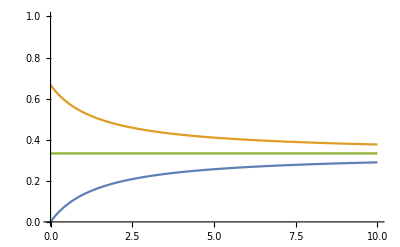

```mathematica
subs = {σ1 -> 1, σ2 -> 2, σ0 -> 3};
Plot[{ne /. subs, ng1 /. subs, ng2 /. subs}, {s, 0, 10}, PlotRange->{Automatic, {0, 1}}]
```

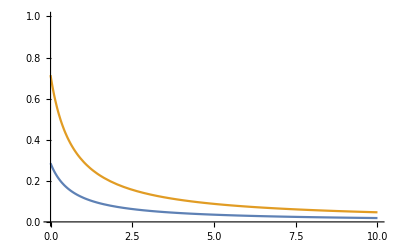

```mathematica
subs = {σ1 ->5, σ2 -> 2, σ0 -> 3};
Plot[{ng1-ne/. subs, ng2-ne/. subs}, {s, 0, 10}, PlotRange->{Automatic, {0, 1}}]
```

### Подстановка σ

```mathematica
ClearAll[Δν, σ1, σ2];
Δν[ν_, ν0_, sign_] := ν - ν0 (1 + sign * v/c);
```

```mathematica
σsubs = {σ1 ->   σ0 1/(4 Δν[ν, ν1, 1]^2/Γ^2+1), σ2 ->   σ0 1/(4 Δν[ν, ν2, -1]^2/Γ^2+1)};
```

```mathematica
ClearAll[c, Γ, ν0, vQ, ν1, ν2]
```

```mathematica
F1 = FullSimplify[f1 /. σsubs ]
F2 = FullSimplify[f2 /. σsubs ]
```

(4.4999×10^16+0.499989 v^2+v (-2.99993×10^8+0.669985 ν)+(-2.00996×10^8+0.224445 ν) ν)/(9.×10^16+6.06001 s+1. v^2+(-4.01996×10^8+0.44889 ν) ν+v (-6.×10^8+1.33999 ν))

(4.5001×10^16+0.500011 v^2+v (-3.00007×10^8+0.67 ν)+(-2.01×10^8+0.224445 ν) ν)/(9.×10^16+6.06001 s+1. v^2+(-4.01996×10^8+0.44889 ν) ν+v (-6.×10^8+1.33999 ν))

## Числа

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3. 10^8; (* м/c *)
Γ = 6. 10^6 /10^6(* МГц *);
vQ = 1200.; (* м/c / c *)

ν1 = ν0-400;
ν2 = ν0 +400;
```

```mathematica
ClearAll[α1, α2];
α1[s_, ν_, v_] := (c^2 (Γ^2+4 ν^2)-8 c (c+v) ν ν1+4 (c+v)^2 ν1^2)/(4 v^2 (ν1^2+ν2^2)+8 c v (ν1^2+ν2^2-ν (ν1+ν2))+c^2 ((2+3 s) Γ^2+4 (2 ν^2+ν1^2+ν2^2-2 ν (ν1+ν2))));
α2[s_, ν_, v_] := (c^2 (Γ^2+4 ν^2)-8 c (c+v) ν ν2+4 (c+v)^2 ν2^2)/(4 v^2 (ν1^2+ν2^2)+8 c v (ν1^2+ν2^2-ν (ν1+ν2))+c^2 ((2+3 s) Γ^2+4 (2 ν^2+ν1^2+ν2^2-2 ν (ν1+ν2))));
```

```mathematica
Manipulate[
Plot[{α1[0, ν0, v], α1[s0, ν0, v], α2[0, ν0, v], α2[s0, ν0, v], α2[s0, ν0, v]+α1[s0, ν0, v]}, {v, -2vQ,2 vQ}, PlotStyle->{{Red, Dashed}, Red, {Blue, Dashed}, Blue, Black}, PlotLegends->{"α_1[0]","α_1[s]","α_2[0]","α_2[s]","α_1[s]+α_2[s]"}  ]
, {s0, 0, 10^5}]
```

```mathematica
ClearAll[FF1, FF2];
FF1[s_, ν_] :=FF1[s, ν] = NIntegrate[
α1[s, ν, v] 1/(1  + 4 (ν - ν1(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, - 2vQ, + 2vQ}, MaxRecursion->20,Exclusions->{0}];
FF2[s_, ν_] :=FF2[s, ν] = NIntegrate[
α2[s, ν, v] 1/(1  + 4 (ν - ν2(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, - 2vQ, + 2vQ}, MaxRecursion->20,Exclusions->{0}];
```

```mathematica
FF1[1,ν0]
FF2[10^5,ν0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in v near {v} = {-267.769}. NIntegrate obtained 5.97784 and 0.000018352 for the integral and error estimates.

5.97784

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in v near {v} = {269.172}. NIntegrate obtained 1.14861 and 2.22204×10^-6 for the integral and error estimates.

1.14861

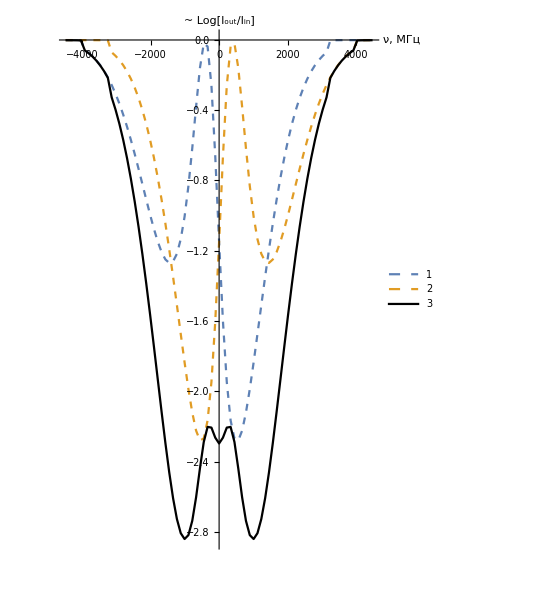

```mathematica
ϵ =10 10^-6;
(*Manipulate[*)
deg=5;
s0 = 10^deg;
DiscretePlot[{-FF1[s0, ν0+ν], -FF2[s0, ν0 + ν], -FF1[s0, ν0+ν]-FF2[s0, ν0 + ν]}
, {ν,-  ϵ ν0,  ϵ ν0 ,  ϵ ν0 / 40}, Filling->None, Joined->True, AxesLabel->{"ν, МГц", "~ Log[I_out/I_in]"}, 

PlotStyle->{Dashed, Dashed, Black},AspectRatio->3/2, PlotLegends->Automatic(*, PlotRange->{Automatic, {-4, 0}}*)]
(*, {deg, 1, 7, 0.1}]*)
```

## Пересекаются ли?

```mathematica
ClearAll[irσ1, irσ2];
irσ1[ν_] :=irσ1[ν] = NIntegrate[
1/(4 Δν[ν, ν1, 1]^2/Γ^2+1)Exp[- v^2/vQ^2], {v, - 10vQ, + 10vQ}, MaxRecursion->20,Exclusions->{0}];
irσ2[ν_] :=irσ2[ν] = NIntegrate[
1/(4 Δν[ν, ν2, 1]^2/Γ^2+1)Exp[- v^2/vQ^2], {v, - 10vQ, + 10vQ}, MaxRecursion->20,Exclusions->{0}];
```

```mathematica
irσ1[ν0-400]
```

6.30269

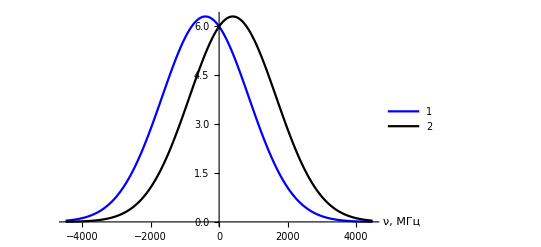

```mathematica
ϵ =10 10^-6;
deg=5;
s0 = 10^deg;
DiscretePlot[{irσ1[ν0 + ν],irσ2[ν0 + ν]}
, {ν,-ϵ ν0, ϵ ν0, ϵ ν0/100}, Filling->None, Joined->True, AxesLabel->{"ν, МГц", ""}, 

PlotStyle->{Blue, Black}, PlotLegends->Automatic]
```

```mathematica
ClearAll[Δν, σ1, σ2];
Δν[ν_, ν0_, sign_] := ν - ν0 (1 + sign * v/c);
```

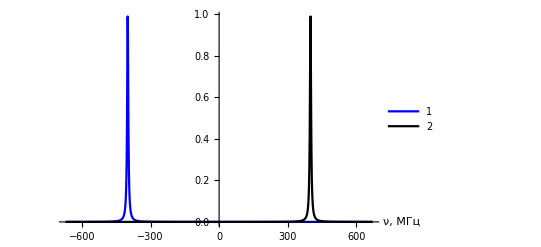

```mathematica
v = 0;
ϵ =1.5 10^-6;
DiscretePlot[{1/(4 Δν[ν0 + ν, ν1, 1]^2/Γ^2+1),1/(4 Δν[ν0 + ν, ν2, 1]^2/Γ^2+1)}
, {ν,-ϵ ν0, ϵ ν0, ϵ ν0/500}, Filling->None, Joined->True, AxesLabel->{"ν, МГц", ""}, 

PlotStyle->{Blue, Black}, PlotLegends->Automatic, PlotRange->Full]
```